# 3D Graphics

Lesson: 3D  Graphicshttps://vimeo.com/ondemand/mathematica/808866812Nonehttps://vimeo.com/ondemand/mathematica/808866812HyperlinkActionRecycledHyperlinkActive
Course: Mathematica Essentials

## Primitives

```mathematica
Graphics3D[{
Point[{0,0,0}], Sphere[{1,0,0},0.5],Torus[{0,3,0},{0.5,1}]
}]
```

-Graphics3D-

## 2D vs 3D

```mathematica
Graphics[{
Point[{0,0}], Line[{{1,0},{0,1},{-1,0},{0,-1}}]
}]
```

-Graphics-

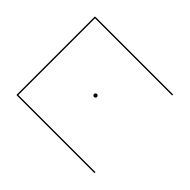

```mathematica
Graphics[{
Point[{0,0}], Line[{{1,0,0},{0,1},{-1,0},{0,-1}}]
}]
```

```mathematica
Graphics[{Tetrahedron[]}]
```

-Graphics-

```mathematica
points=Table[{Cos[u],Sin[u],u},{u,1,10,0.3}];
Graphics3D[{
Point[points],Sphere[{0,0,0},1]
}]
```

-Graphics3D-

```mathematica
Graphics3D[{
Point[{0,0}]
}]
```

-Graphics3D-

```mathematica
Graphics3D[{Sphere[],Sphere[{2,0,0},1]}]
```

-Graphics3D-

```mathematica
Graphics3D[{Sphere[],Circle[],Sphere[{2,0,0},1]}]
```

-Graphics3D-

## Options

```mathematica
Graphics3D[{
Sphere[],Cylinder[{{3,0,0},{2,2,0}}]
},Boxed->False,Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
Partition[Options[Graphics3D],3]//TableForm
```

AlignmentPoint→Center | AspectRatio→Automatic | AutomaticImageSize→False
Axes→False | AxesEdge→Automatic | AxesLabel→None
AxesOrigin→Automatic | AxesStyle→{} | Background→None
BaselinePosition→Automatic | BaseStyle→{} | Boxed→True
BoxRatios→Automatic | BoxStyle→{} | ClipPlanes→None
ClipPlanesStyle→Automatic | ColorOutput→Automatic | ContentSelectable→Automatic
ControllerLinking→False | ControllerMethod→Automatic | ControllerPath→Automatic
CoordinatesToolOptions→Automatic | DisplayFunction:>$DisplayFunction | Epilog→{}
FaceGrids→None | FaceGridsStyle→{} | FormatType:>TraditionalForm
ImageMargins→0. | ImagePadding→All | ImageSize→Automatic
ImageSizeRaw→Automatic | LabelStyle→{} | Lighting→Automatic
Method→Automatic | PlotLabel→None | PlotRange→All
PlotRangePadding→Automatic | PlotRegion→Automatic | PreserveImageOptions→Automatic
Prolog→{} | RotationAction→Fit | SphericalRegion→Automatic
Ticks→Automatic | TicksStyle→{} | TouchscreenAutoZoom→False
ViewAngle→Automatic | ViewCenter→Automatic | ViewMatrix→Automatic
ViewPoint→{1.3,-2.4,2.} | ViewProjection→Automatic | ViewRange→All

## Directives

```mathematica
Graphics3D[{Opacity[0.3],Sphere[],RGBColor["#aaff33"],Opacity[1],Cube[]}
,Boxed->False]
```

-Graphics3D-

## Edges & Faces

```mathematica
blueGlass=FaceForm[{Opacity[0.3],Darker[Blue]}];
greenEdge=EdgeForm[{Thickness[0.01],Darker[Green]}];
Graphics3D[{
blueGlass, greenEdge,Icosahedron[]
},Boxed->False]
```

-Graphics3D-

## Materials

```mathematica
Graphics3D[{
MaterialShading[<|
"BaseColor"->Green,"RoughnessCoefficient"->0.1,"MetallicCoefficient"->0.5|>],
Torus[]
},Boxed->False]
```

-Graphics3D-

## Lighting

```mathematica
Graphics3D[{PointLight[White,{0,0,0}],
PointLight[Red,{0,0,-3}],DirectionalLight[Green,{2,1,3}],SpotLight[Yellow,{{3,1,2},{0,0,0}},10Degree],
MaterialShading["Gold"],Cube[],
MaterialShading["Plastic"],Sphere[{2,0,0},0.5], 
MaterialShading["Silver"],Octahedron[{0,2,0}],
MaterialShading["Clay"],Torus[{2,2,1},{1/2,1}]
},Boxed->False,Lighting->None,SphericalRegion->True]
```

-Graphics3D-